0≤a≤π/9

Minimize::natt: The minimum is not attained at any point satisfying the given constraints.

Minimum absolu Niveau 1: {-0.159155,{a→0.}}

Minimum absolu Niveau 2: {-∞,{a→0.}}

Minimum absolu Niveau 3: {-0.159155,{a→0.}}

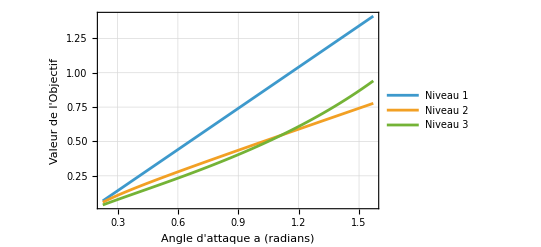

```mathematica
(*1. Définition des paramètres*)cl=1;
L=3;

(*2. Définition des fonctions d'allongement (Lambda)*)
lambda1[a_]:=2*cl/(2*Pi*a-cl);
lambda2[a_]:=8*a*Pi*cl/(-cl^2+4*a^2*Pi^2);
lambda3[a_]:=((2*cl-a*Pi)+Sqrt[4*Pi*a*cl+a*Pi^2])/(2*a*Pi-cl);

(*3. Définition des fonctions objectifs (Traînée+Pénalité de niveau)*)
obj1[a_]:=cl^2/(Pi*lambda1[a]);
obj2[a_]:=cl^2/(Pi*lambda2[a])
obj3[a_]:=cl^2/(Pi*lambda3[a]);

(*4. Domaine de recherche (de 13 degrés à 90 degrés,en radians)*)
domaine=0*Pi/180<=a<=20 * Pi/180

(*5. Recherche analytique stricte des minimums*)
min1=Minimize[{obj1[a],domaine},a];
min2=Minimize[{obj2[a],domaine},a];
min3=Minimize[{obj3[a],domaine},a];

(*6. Affichage des résultats numériques*)
Print["Minimum absolu Niveau 1: ",N[min1]];
Print["Minimum absolu Niveau 2: ",N[min2]];
Print["Minimum absolu Niveau 3: ",N[min3]];

(*7. Tracé des courbes pour visualiser l'absence de creux*)
Plot[{obj1[a],obj2[a],obj3[a]},{a,13*Pi/180,Pi/2},PlotLegends->{"Niveau 1","Niveau 2","Niveau 3"},AxesLabel->{"Angle d'attaque a (radians)","Valeur de l'Objectif"},PlotTheme->"Detailed",PlotRange->All]
```